# Jakub Zbrzezny Numer indeksu: 286689 Numer na liście obecności: 1

Rozważamy problem zachowania podwójnego wahadła matematycznego, jak na poniższym rysunku.

-Graphics-

Wiemy, że:
L_1 = 5, L_2  = 3 (L_1, L_2 to długości dwóch części wahadła),
m_1 = 5, m_2 = 1 (m_1, m_2 to masy zawieszone na wahadle),
θ_(1,0)= π/3(θ_(1,0)= θ_1(0)),
θ_(2,0) = π/4(θ_(2,0) = θ_2(0))
a szukamy funkcji θ_1(t) i θ_2(t) opisujących zmianę w czasie kątów widocznych na rysunku. Zakładamy, że wahadło zostaje puszczone swobodnie, tzn. z zerową prędkością początkową.
-Graphics-
Przyjmujemy, że g = 9,81.
Punkt (0,0) jest punktem zaczepienia wahadła o długości L_1. 
Współrzędne ciała o masie m_1 w czasie t wynoszą R_1(t) = (L_1 sin(θ_1(t)), - L_1 cos(θ_1(t))).
Na ciało o masie m_1 działa siła grawitacji F_g1=(0, - m_1 g) oraz siła naciągu liny o długości L_1. 
Wartość tej siły naciągu wynosi - T_1/L_1R_1(t).
Współrzędne ciała o masie m_2 w czasie t wynoszą R_2(t) = R_1(t) + (L_2 sin(θ_2(t)), - L_2 cos(θ_2(t))).
Na ciało o masie m_2 działa siła grawitacji F_g2 = (0, - m_2 g) oraz siła naciągu liny o długości L_2. Wartość tej siły naciągu jest równa (- T_2 (R_2(t) - R_1(t)))/L_2.
Siła wypadkowa działająca na ciało o masie m_1 wynosi F_1 =  T_1 - T_2 + F_g1, a na ciało o masie m_2 F_2= T_2 + F_g2.

```mathematica
g = 9.81; L1 = 5; L2 = 3; m1 = 5; m2 = 1;
```

```mathematica
R1[t_]={L1 Sin[θ1[t]], - L1 Cos[θ1[t]]};
```

```mathematica
R2[t_] = R1[t] + {L2 Sin[θ2[t]], - L2 Cos[θ2[t]]};
```

```mathematica
F1[t_]=-T1/L1 R1[t] + T2/L2 ( R2[t] - R1[t]) + {0, - m1 g};
```

```mathematica
F2[t_] = - T2/L2(R2[t] - R1[t]) + {0, - m2 g};
```

```mathematica
eq1 = m1 R1''[t] - F1[t];
```

```mathematica
eq2 = m2 R2''[t] - F2[t];
```

```mathematica
EQ1 = Simplify[eq1[[1]] Cos[θ1[t]] + eq1[[2]] Sin[θ1[t]] + eq2[[1]] Cos[θ1[t]] + eq2[[2]] Sin[θ1[t]]]
```

58.86 Sin[θ1[t]]+3. Sin[θ1[t]-θ2[t]] θ2'[t]^2+30. θ1''[t]+3. Cos[θ1[t]-θ2[t]] θ2''[t]

```mathematica
EQ2 = Simplify[eq2[[1]] Cos[θ2[t]] + eq2[[2]] Sin[θ2[t]]]
```

9.81 Sin[θ2[t]]-5. Sin[θ1[t]-θ2[t]] θ1'[t]^2+5. Cos[θ1[t]-θ2[t]] θ1''[t]+3. θ2''[t]

θ1 ’ [0] = θ2 ’ [0] = 0, bo wahadło jest puszczone z zerową prędkością początkową.

```mathematica
solution = NDSolve[{EQ1==0, EQ2 ==0, θ1[0] == π/3, θ2[0] == π/4, θ1'[0] == 0, θ2'[0]==0},{θ1[t], θ2[t]}, {t,0,20}];
```

Wykresy rozwiązań θ_1(t), θ_2(t):

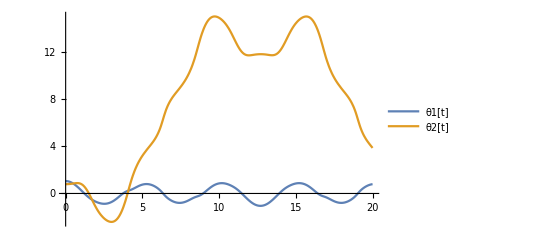

```mathematica
Plot[Evaluate[{θ1[t],θ2[t]}/.solution],{t,0,20},PlotLegends->{"θ1[t]","θ2[t]"}]
```

Tworzymy animację ruchu naszego wahadła matematycznego.

```mathematica
r1[t_] = Evaluate[{L1 Sin[θ1[t]], - L1 Cos[θ1[t]]}/.solution[[1]]];
```

```mathematica
r2[t_] = r1[t] + Evaluate[{L2 Sin[θ2[t]], - L2 Cos [θ2[t]]}/.solution[[1]]];
```

```mathematica
Manipulate[
Show[
Graphics[{Black, Dashed, Line[{{0,0},{0,-8}}]}],
Graphics[{Orange,Thick,Line[{{0,0},r1[t],r2[t]}]}],
ParametricPlot[r2[s],{s,0,t}],
Graphics[{PointSize[0.03],Red,Point[r1[t]],Point[r2[t]]}],
PlotRange->{{-6,6},{-7,1}}
],
{t,0.01,20}]
```